```mathematica
pics={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
(*Place the teacup in the region (x>0,y>0,z>0). The spout touches the plane y=0, and the base touches the plane z=0*)
```

```mathematica
(*This just collects the pixel data for each image. Since it is greyscale,r=g=b. The alpha (transparency ) channel is different tough. *) dat=Table[ImageData[pics⟦i⟧],{i,1,5}];
(*The dimensions of the images are found using Dimensions[]*)
dim=Dimensions[dat]
```

{5,480,640,4}

```mathematica
(*First we test the scale of the image. If there is a major difference in the size of the picture from different perspectives, we have an issue*)
```

```mathematica
For[i=1,i<6,i++,xmin[i]=dim⟦2⟧;xmax[i]=1;ymin[i]=dim⟦3⟧;ymax[i]=1]
For[i=1,i<6,i++,
For[x=1,x≤ dim⟦2⟧,x++,
For[y=1,y≤ dim⟦3⟧,y++,
If[dat⟦i,x,y,4⟧>0,If[x>xmax[i],xmax[i]=x];If[x<xmin[i],xmin[i]=x];If[y>ymax[i],ymax[i]=y];If[y<ymin[i],ymin[i]=y]]]]];
(*This shows the left and right as well at upper and lower most egdes of the object*)
Table[{xmax[i],xmin[i],ymax[i],ymin[i]},{i,1,5}]
(*We see that the legnth width and height of the teapot are consistent*)
Table[{xmax[i]-xmin[i],ymax[i]-ymin[i]},{i,1,5}]
```

{{387,97,503,135},{387,97,506,138},{387,97,612,20},{387,97,621,29},{426,58,621,29}}

{{290,368},{290,368},{290,592},{290,592},{368,592}}

```mathematica
(*We the largest value for each image may be useful*) max=Table[Max[dat⟦i,All,All,1⟧],{i,1,5}]
```

{0.976471,0.968627,0.788235,0.788235,1.}

```mathematica
i=1;
s={};
For[x=xmin[i],x<xmax[i]+1,x++,
For[y=ymin[i],y<ymax[i]+1,y++,
If[dat⟦i,x,y,1⟧>0&&(Abs[dat⟦i,x+1,y,1⟧-dat⟦i,x-1,y,1⟧]>0.05||Abs[dat⟦i,x,y+1,1⟧-dat⟦i,x,y-1,1⟧]>0.05),s=Append[s,{ymax[i]-y,α(max⟦i⟧-dat⟦i,x,y,1⟧ ),xmax[i]-x}]]]]
```

```mathematica
i=2;
t={};
For[x=xmin[i],x<xmax[i]+1,x++,
For[y=ymin[i],y<ymax[i]+1,y++,
If[dat⟦i,x,y,1⟧>0&&(Abs[dat⟦i,x+1,y,1⟧-dat⟦i,x-1,y,1⟧]>0.05||Abs[dat⟦i,x,y+1,1⟧-dat⟦i,x,y-1,1⟧]>0.05),t=Append[t,{ymax[i]-y,592-α(max⟦i⟧-dat⟦i,x,y,1⟧ ),xmax[i]-x}]]]]
```

```mathematica
i=3;
u={};
For[x=xmin[i],x<xmax[i]+1,x++,
For[y=ymin[i],y<ymax[i]+1,y++,
If[dat⟦i,x,y,1⟧>0&&(Abs[dat⟦i,x+1,y,1⟧-dat⟦i,x-1,y,1⟧]>0.05||Abs[dat⟦i,x,y+1,1⟧-dat⟦i,x,y-1,1⟧]>0.05),u=Append[u,{α(max⟦i⟧-dat⟦i,x,y,1⟧),y-ymin[i],xmax[i]-x}]]]]
```

```mathematica
i=4;
v={};
For[x=xmin[i],x<xmax[i]+1,x++,
For[y=ymin[i],y<ymax[i]+1,y++,
If[dat⟦i,x,y,1⟧>0&&(Abs[dat⟦i,x+1,y,1⟧-dat⟦i,x-1,y,1⟧]>0.05||Abs[dat⟦i,x,y+1,1⟧-dat⟦i,x,y-1,1⟧]>0.05),v=Append[v,{368-α(max⟦i⟧-dat⟦i,x,y,1⟧),ymax[i]-y,xmax[i]-x}]]]]
```

```mathematica
i=5;
w={};
For[x=xmin[i],x<xmax[i]+1,x++,
For[y=ymin[i],y<ymax[i]+1,y++,
If[dat⟦i,x,y,1⟧>0&&(Abs[dat⟦i,x+1,y,1⟧-dat⟦i,x-1,y,1⟧]>0.05||Abs[dat⟦i,x,y+1,1⟧-dat⟦i,x,y-1,1⟧]>0.05),w=Append[w,{xmax[i]-x,ymax[i]-y,290-α(max⟦i⟧-dat⟦i,x,y,1⟧)}]]]]
```

```mathematica
α1=525;
Show[ListPointPlot3D[(Join[s,t]/.α->α1),BoxRatios->{290,592,368}],ListPointPlot3D[(Join[u,v]/.α->α1),BoxRatios->{290,592,368},PlotStyle->Red],ListPointPlot3D[(w/.α->α1),BoxRatios->{290,592,368},PlotStyle->Green]]
```

-Graphics3D-

```mathematica
Max[Coefficient[s⟦All,2⟧,α[1]]]
```

0.976471

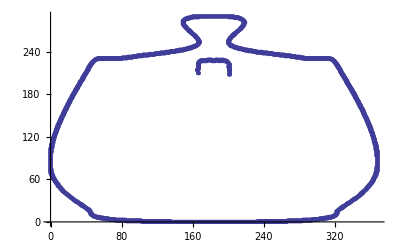

```mathematica
ListPlot[s]
```

```mathematica
xmin[i]
```

97

```mathematica
dat⟦i,All,All,1⟧
```

```mathematica
s
```

{}